```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3+c04 x^4, 0≤x≤1/2}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3+c14(x-1)^4, 1/2<x≤3/2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3+c24(x-2)^4, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Continuity*)
C1l=Simplify[h[x],0≤x≤1/2]/.x->1/2
C1r=Simplify[h[x],1/2<x≤3/2]/.x->1/2
C2l=Simplify[h[x],1/2<x≤3/2]/.x->3/2
C2r=Simplify[h[x],3/2<x≤5/2]/.x->3/2
C3l=Simplify[h[x],3/2<x≤5/2]/.x->5/2
```

1+c01/2+c02/4+c03/8+c04/16

1/2 (-c11+1/2 (c12+1/2 (-c13+c14/2)))

1/2 (c11+1/2 (c12+1/2 (c13+c14/2)))

1/2 (-c21+1/2 (c22+1/2 (-c23+c24/2)))

1/2 (c21+1/2 (c22+1/2 (c23+c24/2)))

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c01,c02+2 (c12+c22),c03,c04+2 (c14+c24)}

{0,-2 c11-4 c21,0,-2 (c13+2 c23)}

```mathematica
(*Smoothness*)
S0=Simplify[D[h[x],x],0<x<1/2]/.x->0
S1l=Simplify[D[h[x],x],0<x<1/2]/.x->1/2
S1r=Simplify[D[h[x],x],1/2<x<3/2]/.x->1/2
S2l=Simplify[D[h[x],x],1/2<x<3/2]/.x->3/2
S2r=Simplify[D[h[x],x],3/2<x<5/2]/.x->3/2
S3l=Simplify[D[h[x],x],3/2<x<5/2]/.x->5/2
```

c01

c01+1/2 (2 c02+1/2 (3 c03+2 c04))

c11+1/2 (-2 c12+1/2 (3 c13-2 c14))

c11+1/2 (2 c12+1/2 (3 c13+2 c14))

c21+1/2 (-2 c22+1/2 (3 c23-2 c24))

c21+1/2 (2 c22+1/2 (3 c23+2 c24))

```mathematica
GenSols=Solve[{
	C1l==C1r,
	C2l==C2r,
	C3l==0,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T0[[5]]==0,
	T1[[2]]==1,
	T1[[4]]==0,
	S0==0,
	S1l==S1r,
	S2l==S2r,
	S3l==0
	},
	{c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c01→0,c03→0,c11→-13/6-(11 c02)/12-(13 c04)/48,c12→13/6+(2 c02)/3+c04/3,c13→8/3+(5 c02)/3+(7 c04)/12,c14→-14/3-(8 c02)/3-(4 c04)/3,c21→5/6+(11 c02)/24+(13 c04)/96,c22→-13/6-(7 c02)/6-c04/3,c23→-4/3-(5 c02)/6-(7 c04)/24,c24→14/3+(8 c02)/3+(5 c04)/6}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
SumF1=SumF1/.φ->1/2;
```

```mathematica
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>3-1/2&&y<4-1/2]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-3-1/2&&y<-2-1/2]
}];
```

```mathematica
TableForm[{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}]
TableForm[{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}]
```

(96 (48-3 (136+44 c02+13 c04) y-8 (13+22 c02+2 c04) y^2+12 (32+20 c02+7 c04) y^3+16 (14+8 c02-5 c04) y^4)-16 x^4 (1+2 y) (32 c02^2 y (-77-90 y+320 y^2)+c04^2 y (-13-918 y+1864 y^2)+448 (-3-22 y-21 y^2+70 y^3)+2 c04 (240-1361 y-2586 y^2+6608 y^3)+4 c02 (-192-(2486+193 c04) y-6 (434+123 c04) y^2+32 (280+59 c04) y^3))+8 x^2 (1+2 y) (2 c04^2 y (-91-138 y+472 y^2)+8 c02^2 y (-451-78 y+976 y^2)+416 (-3-22 y-21 y^2+70 y^3)+c04 (-192-2591 y-3138 y^2+10616 y^3)+2 c02 (-1056-(4778+841 c04) y-54 (58+5 c04) y^2+8 (1894+281 c04) y^3))+4 x^3 (7 c04^2 y (169-112 y-364 y^2+16 y^3)+80 c02^2 y (143-164 y-260 y^2+224 y^3)+256 (-36+163 y-91 y^2-208 y^3+196 y^4)+8 c04 (-252+1817 y-1085 y^2-2912 y^3+1436 y^4)+8 c02 (-720+(5548+923 c04) y-2 (2222+427 c04) y^2-260 (32+7 c04) y^3+8 (938+103 c04) y^4))+x (-13 c04^2 y (169-112 y-364 y^2+16 y^3)-176 c02^2 y (143-164 y-260 y^2+224 y^3)-256 (-153+517 y-364 y^2-652 y^3+784 y^4)-8 c04 (-468+4238 y-2975 y^2-7268 y^3+3524 y^4)-8 c02 (-1584+11 (1304+169 c04) y-2 (6890+841 c04) y^2-4 (5548+923 c04) y^3+8 (2870+193 c04) y^4)))/36864
(-16 c02^2 x (-1+y) (x (786-4856 y+5416 y^2-1632 y^3)+11 (-27+42 y+4 y^2-8 y^3)+20 x^2 (27-42 y-4 y^2+8 y^3)+8 x^3 (3+412 y-596 y^2+192 y^3))+c04^2 x (-1+y) (-13 (-99+300 y-268 y^2+80 y^3)+28 x^2 (-99+300 y-268 y^2+80 y^3)-4 x (-321+760 y-692 y^2+240 y^3)+16 x^3 (-519+1732 y-1652 y^2+504 y^3))-32 (x (72-561 y+689 y^2+72 y^3-140 y^4)+8 x^3 (-18+45 y-37 y^2-48 y^3+28 y^4)-12 (54-307 y+525 y^2-356 y^3+84 y^4)-13 x^2 (12-277 y+489 y^2-344 y^3+84 y^4)+28 x^4 (12-277 y+489 y^2-344 y^3+84 y^4))+2 c04 (x (-5229+20916 y-29285 y^2+16764 y^3-3556 y^4)+x^2 (-3789+5189 y-3228 y^2+1108 y^3-432 y^4)+6 (315-1699 y+2820 y^2-1868 y^3+432 y^4)+4 x^3 (1710-6699 y+9347 y^2-5232 y^3+1084 y^4)+4 x^4 (4095-15587 y+23304 y^2-14524 y^3+3360 y^4))+8 c02 (6 (249-1421 y+2424 y^2-1636 y^3+384 y^4)+4 x^3 (522-1329 y+793 y^2+432 y^3-268 y^4+c04 (342-1239 y+1553 y^2-828 y^3+172 y^4))-x (1647-4644 y+3367 y^2+588 y^3-628 y^4+c04 (720-2643 y+3371 y^2-1836 y^3+388 y^4))+4 x^4 (-171+7295 y-14880 y^2+11020 y^3-2688 y^4+c04 (723-2675 y+3564 y^2-2092 y^3+480 y^4))+x^2 (2385-26633 y+49716 y^2-34756 y^3+8208 y^4+c04 (69-2077 y+4428 y^2-3092 y^3+672 y^4))))/9216
(48 (1+x) (3+2 x)^2 (32+7 c04+112 x+20 c04 x+4 c02 (5+16 x)) (1+c02 (-1+y)^2+c04 (-1+y)^4)+48 (1+c02 (1+x)^2+c04 (1+x)^4) (3-2 y)^2 (-1+y) (-32-7 c04+112 y+20 c04 y+4 c02 (-5+16 y))+4 (1+x) (3+2 x)^2 (32+7 c04+112 x+20 c04 x+4 c02 (5+16 x)) (3-2 y)^2 (-1+y) (-32-7 c04+112 y+20 c04 y+4 c02 (-5+16 y))-7 (1+x) (8 (18+103 x+100 x^2+28 x^3)+4 c02 (33+128 x+116 x^2+32 x^3)+c04 (63+232 x+220 x^2+64 x^3)) (3-2 y)^2 (-1+y) (-32-7 c04+112 y+20 c04 y+4 c02 (-5+16 y))-7 (1+x) (3+2 x)^2 (32+7 c04+112 x+20 c04 x+4 c02 (5+16 x)) (-1+y) (8 (-18+103 y-100 y^2+28 y^3)+4 c02 (-33+128 y-116 y^2+32 y^3)+c04 (-63+232 y-220 y^2+64 y^3))+2 (1+x) (8 (18+103 x+100 x^2+28 x^3)+4 c02 (33+128 x+116 x^2+32 x^3)+c04 (63+232 x+220 x^2+64 x^3)) (-1+y) (8 (-18+103 y-100 y^2+28 y^3)+4 c02 (-33+128 y-116 y^2+32 y^3)+c04 (-63+232 y-220 y^2+64 y^3)))/36864
((1+x) (-2+y) (7 (3+2 x)^2 (32+7 c04+112 x+20 c04 x+4 c02 (5+16 x)) (5-2 y)^2 (16 (-9+7 y)+c04 (-27+20 y)+c02 (-84+64 y))-2 (8 (18+103 x+100 x^2+28 x^3)+4 c02 (33+128 x+116 x^2+32 x^3)+c04 (63+232 x+220 x^2+64 x^3)) (5-2 y)^2 (16 (-9+7 y)+c04 (-27+20 y)+c02 (-84+64 y))-2 (3+2 x)^2 (32+7 c04+112 x+20 c04 x+4 c02 (5+16 x)) (8 (-249+387 y-184 y^2+28 y^3)+4 c02 (-309+456 y-212 y^2+32 y^3)+c04 (-579+864 y-412 y^2+64 y^3))))/73728
((2+x) (5+2 x)^2 (16 (9+7 x)+c04 (27+20 x)+c02 (84+64 x)) (5-2 y)^2 (-2+y) (16 (-9+7 y)+c04 (-27+20 y)+c02 (-84+64 y)))/73728
0

(16 c02^2 (-1+x) y (3 (-649+804 y+1180 y^2-3552 y^3)+32 x^3 (77-244 y-140 y^2+640 y^3)+4 x (2827-3236 y-5140 y^2+11168 y^3)-4 x^2 (2563-5036 y-4660 y^2+14240 y^3))+c04^2 (-1+x) y (-1287+8304 y+2772 y^2-44304 y^3+16 x^3 (13-944 y-28 y^2+3728 y^3)+8 x (1079-4240 y-2324 y^2+20368 y^3)-4 x^2 (1339-10544 y-2884 y^2+44624 y^3))+256 (x (-21-3847 y+4862 y^2+4252 y^3-10472 y^4)+28 x^4 (-3+28 y-65 y^2-28 y^3+140 y^4)+6 (12+67 y-156 y^2-76 y^3+336 y^4)-4 x^3 (-48+947 y-1729 y^2-992 y^3+3724 y^4)+x^2 (-33+6296 y-8983 y^2-6836 y^3+19348 y^4))+8 c04 (x (-6780-25712 y+58243 y^2+41972 y^3-155284 y^4)+3 (564+1037 y-3785 y^2-1592 y^3+10124 y^4)+4 x^4 (240+881 y-5308 y^2-1436 y^3+13216 y^4)-4 x^3 (1212+5341 y-20147 y^2-8656 y^3+51428 y^4)+x^2 (8976+39973 y-106052 y^2-65068 y^3+278720 y^4))+8 c02 (8 x^4 (-1+2 y) (192-(2486+193 c04) y+6 (434+123 c04) y^2+32 (280+59 c04) y^3)+3 (624+(5148+565 c04) y-2 (4854+559 c04) y^2-4 (1704+289 c04) y^3+8 (3090+811 c04) y^4)+2 x^2 (768+(95278+9329 c04) y-4 (35618+4975 c04) y^2-20 (6554+955 c04) y^3+32 (11086+2537 c04) y^4)-4 x^3 (-816+(28508+2467 c04) y-2 (28082+4069 c04) y^2-4 (9584+1279 c04) y^3+8 (16982+3673 c04) y^4)+x (-5136-(116512+12029 c04) y+2 (76066+9797 c04) y^2+20 (8108+1225 c04) y^3-8 (48142+11813 c04) y^4)))/36864
(16 c02^2 (-1+x) (1+y) (3 (351+646 y+204 y^2+8 y^3)+8 x^3 (-3+412 y+596 y^2+192 y^3)-4 x^2 (-153+2262 y+3596 y^2+1192 y^3)+2 x (-969+1676 y+4524 y^2+1648 y^3))-c04^2 (-1+x) (1+y) (16 x^3 (519+1732 y+1652 y^2+504 y^3)-3 (2835+9724 y+9228 y^2+2768 y^3)-4 x^2 (6921+22884 y+21700 y^2+6608 y^3)+4 x (7293+24224 y+22884 y^2+6928 y^3))+32 (12 (-21+56 y+119 y^2+100 y^3+28 y^4)+28 x^4 (12+277 y+489 y^2+344 y^3+84 y^4)-8 x^3 (150+3833 y+6809 y^2+4864 y^3+1204 y^4)-x (672+23303 y+41855 y^2+30664 y^3+7756 y^4)+x^2 (1428+41855 y+74907 y^2+54472 y^3+13692 y^4))-2 c04 (9 (1788+8137 y+12779 y^2+8040 y^3+1820 y^4)+4 x^4 (4095+15587 y+23304 y^2+14524 y^3+3360 y^4)-4 x^3 (18090+69047 y+102563 y^2+63328 y^3+14524 y^4)-x (73233+298486 y+449287 y^2+276188 y^3+62348 y^4)+x^2 (115011+449287 y+668232 y^2+410252 y^3+93216 y^4))-8 c02 (-9 (-404-739 y-505 y^2+72 y^3+76 y^4)-4 x^4 (171+7295 y+14880 y^2+11020 y^3+2688 y^4)+4 x^3 (162+27851 y+58727 y^2+44512 y^3+11020 y^4)+x (-6651+52150 y+132499 y^2+111404 y^3+29180 y^4)-x^2 (-4545+132499 y+297888 y^2+234908 y^3+59520 y^4)+c04 (-1+x) (1+y) (4 x^3 (723+1952 y+1612 y^2+480 y^3)-3 (1203+3827 y+3348 y^2+964 y^3)-4 x^2 (2511+6753 y+5492 y^2+1612 y^3)+x (11481+32608 y+27012 y^2+7808 y^3))))/9216
(16 c02^2 (-2+x) (1+y) (4 x^3 (327+1308 y+1180 y^2+320 y^3)-4 x^2 (2142+8623 y+7840 y^2+2140 y^3)-3 (4014+16373 y+15120 y^2+4180 y^3)+x (18123+73468 y+67356 y^2+18512 y^3))+c04^2 (-2+x) (1+y) (32 x^3 (111+429 y+410 y^2+118 y^3)-4 x^2 (5727+22174 y+21220 y^2+6112 y^3)-3 (10557+41090 y+39468 y^2+11392 y^3)+2 x (23907+92792 y+88956 y^2+25648 y^3))+16 (28 x^4 (84+621 y+1039 y^2+648 y^3+140 y^4)-8 x^3 (2544+18623 y+31181 y^2+19504 y^3+4228 y^4)+12 (3597+25691 y+43073 y^2+27088 y^3+5908 y^4)-11 x (8004+57697 y+96715 y^2+60776 y^3+13244 y^4)+x^2 (64572+468519 y+784973 y^2+492312 y^3+107044 y^4))+c04 (4 x^4 (6723+37071 y+59296 y^2+37356 y^3+8288 y^4)+18 (26304+145713 y+234243 y^2+148336 y^3+33052 y^4)-4 x^3 (56952+314269 y+503263 y^2+317456 y^3+70508 y^4)+x^2 (710991+3926991 y+6296540 y^2+3977244 y^3+884368 y^4)-x (962811+5324348 y+8548127 y^2+5406652 y^3+1203532 y^4))+4 c02 (4 x^4 (3633+21381 y+34040 y^2+20868 y^3+4480 y^4)+18 (14744+86591 y+139029 y^2+86288 y^3+18756 y^4)-4 x^3 (31176+183335 y+292589 y^2+180016 y^3+38788 y^4)+x^2 (393717+2313669 y+3701164 y^2+2285076 y^3+494096 y^4)-x (537705+3158236 y+5062693 y^2+3135092 y^3+679940 y^4)+c04 (-2+x) (1+y) (4 x^3 (1125+4440 y+4180 y^2+1184 y^3)-4 x^2 (7287+28855 y+27244 y^2+7732 y^3)-3 (13461+53753 y+51108 y^2+14572 y^3)+x (61035+242680 y+229932 y^2+65408 y^3))))/4608
(-64 c04 (-2+x) (2+y) (4 x^3 (9891+15546 y+7724 y^2+1232 y^3)-9 (35250+55425 y+27550 y^2+4396 y^3)-2 x^2 (123975+194882 y+96840 y^2+15448 y^3)+x (498825+784240 y+389764 y^2+62184 y^3))-16 c02^2 (-2+x) (2+y) (256 x^3 (633+1002 y+500 y^2+80 y^3)-4 x^2 (253107+400708 y+199980 y^2+32000 y^3)-3 (426825+675980 y+337476 y^2+54016 y^3)+4 x (506985+802780 y+400708 y^2+64128 y^3))-c04^2 (-2+x) (2+y) (16 x^3 (12435+19440 y+9596 y^2+1520 y^3)+16 x (158955+248560 y+122716 y^2+19440 y^3)-4 x^2 (313959+490864 y+242316 y^2+38384 y^3)-3 (542025+847760 y+418612 y^2+66320 y^3))-256 (28 x^4 (2202+4587 y+3487 y^2+1152 y^3+140 y^4)-64 x^3 (7926+16511 y+12552 y^2+4147 y^3+504 y^4)+6 (161502+336545 y+255869 y^2+84544 y^3+10276 y^4)-11 x (183570+382415 y+290739 y^2+96064 y^3+11676 y^4)+x^2 (1535214+3198129 y+2431373 y^2+803328 y^3+97636 y^4))-8 c02 (-2+x) (2+y) (32 (4 x^3 (8835+13986 y+6988 y^2+1120 y^3)-3 (92850+147015 y+73478 y^2+11780 y^3)-2 x^2 (110217+174490 y+87192 y^2+13976 y^3)+x (441045+698300 y+348980 y^2+55944 y^3))+c04 (8 x^3 (22653+35628 y+17684 y^2+2816 y^3)-4 x^2 (284403+447374 y+222084 y^2+35368 y^3)-3 (485175+763570 y+379204 y^2+60408 y^3)+2 x (1145355+1802080 y+894748 y^2+142512 y^3))))/73728
(-16 c02^2 (7-2 x)^2 (111-85 x+16 x^2) (5+2 y)^2 (42+53 y+16 y^2)-c04^2 (7-2 x)^2 (141-107 x+20 x^2) (5+2 y)^2 (54+67 y+20 y^2)-16 c04 (7-2 x)^2 (-3+x) (2+y) (5+2 y)^2 (-855-649 y+x (369+280 y))-256 (-3157 x (5+2 y)^2 (18+23 y+7 y^2)+1571 x^2 (5+2 y)^2 (18+23 y+7 y^2)-344 x^3 (5+2 y)^2 (18+23 y+7 y^2)+28 x^4 (5+2 y)^2 (18+23 y+7 y^2)+48 (22044+45815 y+34643 y^2+11368 y^3+1372 y^4))-8 c02 (7-2 x)^2 (-3+x) (2+y) (5+2 y)^2 (8 (-669-515 y+x (291+224 y))+c04 (-993-746 y+x (426+320 y))))/73728
1

```mathematica
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5}=Parallelize[{
	Simplify[D[SumF1a1,{{x,y}}]],
	Simplify[D[SumF1a2,{{x,y}}]],
	Simplify[D[SumF1a3,{{x,y}}]],
Simplify[D[SumF1a4,{{x,y}}]],
Simplify[D[SumF1a5,{{x,y}}]],
	Simplify[D[SumF1b1,{{x,y}}]],
	Simplify[D[SumF1b2,{{x,y}}]],
	Simplify[D[SumF1b3,{{x,y}}]],
Simplify[D[SumF1b4,{{x,y}}]],
Simplify[D[SumF1b5,{{x,y}}]]
}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1b1,Err1b2,Err1b3,Err1b4,Err1b5}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-2-1/2)^(-1-1/2) (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(3-1/2)^(4-1/2) (DSumF1b5.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5];
```

```mathematica
Err=Err1
DErr=FullSimplify[D[Err,{{c02,c04}}]];
H=FullSimplify[D[Err,{{c02,c04},2}]];
Sols=Solve[DErr==0,{c02,c04}];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1/5618427494400(256 c02 (200217517472+c02 (118347584160+c02 (27664541552+2303656475 c02)))+256 c02 (63489924552+c02 (22056170070+2442488383 c02)) c04+96 (22972836800+c02 (15775245040+2632493507 c02)) c04^2+16 (8531766382+2890448743 c02) c04^3+3241946411 c04^4+103333888 (291665+133231 c04))

1 | 0.0690686 | True
2 | 0.485241+0.750128 ⅈ | False
3 | 0.485241-0.750128 ⅈ | False
4 | 0.475722+0.71243 ⅈ | False
5 | 0.475722-0.71243 ⅈ | False
6 | 0.606476+2.0615 ⅈ | False
7 | 0.606476-2.0615 ⅈ | False
8 | 1.07829+0.117982 ⅈ | False
9 | 1.07829-0.117982 ⅈ | False

```mathematica
RootReduce[Sols[[1]]]
```

{c02→Root[1689662005856337976240041904499715134372237013891+1913730991673238426329051917073993219776357823234 #1+875576459165396432047441848633307153441108337957 #1^2+220353172042287473274228459981792313551037813848 #1^3+34801416482455760933198507141290225454678189258 #1^4+3691137740398847524505779769450660705708056556 #1^5+269781047608097129415603204681660622987864608 #1^6+13495678805173790703538473545709318352456896 #1^7+431424428610766564410277417438563815617152 #1^8+7052647884593722360448514392761188016896 #1^9&,1],c04→Root[-12052730059666565027942383263597277906151992998912+8724149967135470183666169667339895553162816345600 #1-2307186105966193393075892682083728786314507275328 #1^2+291580584404141632572557804308371318670966217856 #1^3-19458521328012163527706445700672395426531724968 #1^4+806520397583283384374587130856734796383219852 #1^5-21683052237286257632433005453889060211834536 #1^6+387555349882436704314878114069617899997788 #1^7-4358609338880559588643958975730339962778 #1^8+27549405799194227970502009346723390691 #1^9&,1]}

{c01→0.,c03→0.,c11→-0.828758,c12→1.62969,c13→0.524805,c14→-2.51876,c21→0.164379,c22→-0.427537,c23→-0.262402,c24→0.919919,c02→-2.40431,c04→3.19769}

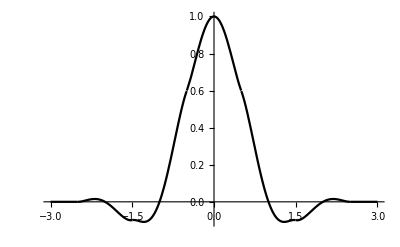

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```